Simulation to the Example 4-7

V(x,y)=∑_(n=-∞)^∞ (exp(nπ/b x)-exp(nπ/b(2a-x)))/(1-exp(2 nπa/b))*(2 V_0)/nπ*sin(nπ/b y), (n∈{Even})

```mathematica
Clear["Global`*"]
a=1;
b=1;
v0=1;
vn[n_]:=If[Mod[n,2]==1,(Exp[(n*Pi)/b*x]-Exp[(n*Pi)/b(2*a-x)])/(1-Exp[2*n*Pi*a/b])*(2v0)/(n*Pi)*Sin[(n*Pi)/b*y],0];
v=Sum[vn[i],{i,-20,20}];
```

Plot the V(x,y), error map and boundary values.

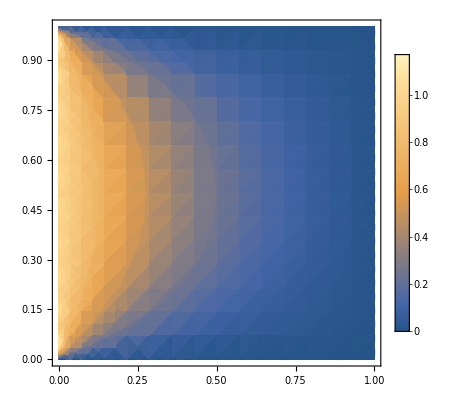
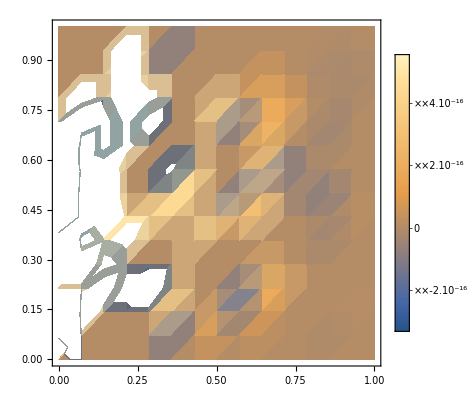
V(x,y) | Error: Δ^2V
-Graphics- | -Graphics-

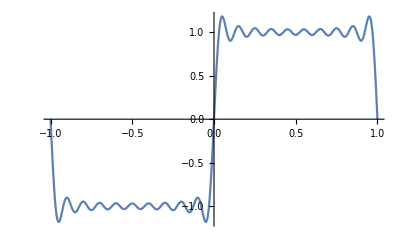
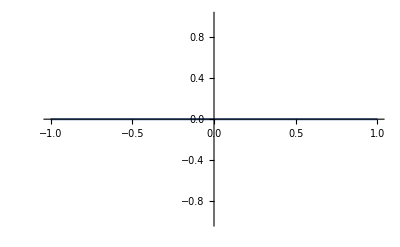
V(0,y) | V(a,y) | V(x,0) | V(x,b)
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
pv=DensityPlot[v,{x,0,1},{y,0,1},PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->{Range[0,1,0.25]},MeshStyle->{Black,Dashed}];
d2x=D[D[v,x],x];
d2y=D[D[v,y],y];
err=DensityPlot[d2x+d2y,{x,0,1},{y,0,1}, PlotLegends->Automatic];
px0=Plot[v/.x->0,{y,-1,1}];
pxa=Plot[v/.x->a,{y,-1,1}];
py0=Plot[v/.y->0,{x,-1,1}];
pyb=Plot[v/.y->b,{x,-1,1}];
funcGrid=Grid[{{"V(x,y)", "Error: Δ^2V"}, {pv, err}}];
boundGrid = Grid[{{"V(0,y)","V(a,y)","V(x,0)","V(x,b)"},{px0, pxa, py0, pyb}}];
Export[ "funcGrid.png", funcGrid];
Export["boundaryGrid.png",boundGrid];
funcGrid
boundGrid
```

Plot the E⃗(x,y)
 E⃗(x,y)=-∇V(x,y)

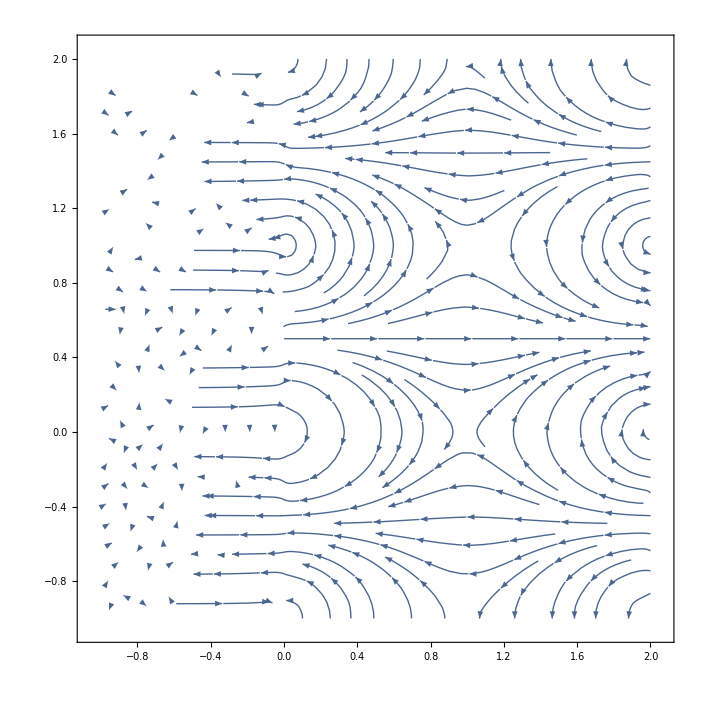

```mathematica
e=-{D[v,x],D[v,y]};
StreamPlot[e,{x,-1,2},{y,-1,2}]
```